This Mathematica code is part of the lecture script Introduction to Computational Quantum Mechanics by Roman Schmied. It is licensed under a Creative Commons Attribution-ShareAlike 4.0 International License.

-Graphics-

You can download the associated lecture script at http://arxiv.org/abs/1403.7050

# transverse Ising model

### quantum-mechanical spin and angular momentum operators

```mathematica
SpinQ[S_]:=IntegerQ[2S]&&S≥0
splus[0]={{0}}//SparseArray;
splus[S_?SpinQ]:=splus[S]= SparseArray[Band[{1,2}]->Table[Sqrt[S(S+1)-M(M+1)],{M,S-1,-S,-1}],{2S+1,2S+1}]
sminus[S_?SpinQ]:=Transpose[splus[S]]
sx[S_?SpinQ]:=sx[S]=(splus[S]+sminus[S])/2
sy[S_?SpinQ]:=sy[S]=(splus[S]-sminus[S])/(2I)
sz[S_?SpinQ]:=sz[S]=SparseArray[Band[{1,1}]->Range[S,-S,-1],{2S+1,2S+1}]
id[S_?SpinQ]:=id[S]=IdentityMatrix[2S+1,SparseArray]
```

### operators acting on many spins

an operator a acting on spin k out of a set of n spins-S:

```mathematica
op[S_?SpinQ,n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2S+1,2S+1}:=KroneckerProduct[IdentityMatrix[(2S+1)^(k-1),SparseArray],a,IdentityMatrix[(2S+1)^(n-k),SparseArray]]
```

spin operators acting on spin k out of a set of n spins-S:

```mathematica
sx[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sx[S]]
sy[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sy[S]]
sz[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sz[S]]
```

### Hamiltonian

transverse Ising model on a ring of N spins:

Ĥ=-b/2∑_(k=1)^N (Ŝ)_x^(k)-∑_(k=1)^(N-1) (Ŝ)_z^(k)(Ŝ)_z^(k+1)

```mathematica
H[S_?SpinQ,n_Integer/;n≥3,b_]:=-b/2 Sum[sx[S,n,k],{k,n}]-Sum[sz[S,n,k].sz[S,n,Mod[k+1,n,1]],{k,n}]
```

### asymptotic ground states

product state θ^(⊗N):

```mathematica
productstate[θ_?VectorQ,1]=θ;
productstate[θ_?VectorQ,n_Integer/;n≥2]:=Flatten[KroneckerProduct@@Table[θ,{n}]]
```

parallel-spin states:

```mathematica
xup[S_?SpinQ]:=2^-S Table[√Binomial[2S,M+S],{M,S,-S,-1}]
xdn[S_?SpinQ]:=2^-S Table[(-1)^(M+S)√Binomial[2S,M+S],{M,S,-S,-1}]
zup[S_?SpinQ]:=SparseArray[1->1,2S+1]
zdn[S_?SpinQ]:=SparseArray[-1->1,2S+1]
```

product states:

```mathematica
allxup[S_?SpinQ,n_Integer/;n≥1]:=productstate[xup[S],n]
allxdn[S_?SpinQ,n_Integer/;n≥1]:=productstate[xdn[S],n]
allzup[S_?SpinQ,n_Integer/;n≥1]:=productstate[zup[S],n]
allzdn[S_?SpinQ,n_Integer/;n≥1]:=productstate[zdn[S],n]
```

### Hamiltonian diagonalization

```mathematica
With[{S=1/2,n=14},
(* Hamiltonian *)
h[b_]=H[S,n,b];
(* two degenerate ground states for b=0 *)
gs0up=allzup[S,n];
gs0dn=allzdn[S,n];
(* ground state for b=+∞ *)
gsplusinf=allxup[S,n];
(* ground state for b=-∞ *)
gsminusinf=allxdn[S,n];
(* numerically calculate lowest m eigenstates *)
Clear[gs];
gs[b_?NumericQ,m_Integer/;m≥1]:=gs[b,m]=-Eigensystem[-h[N[b]],m,Method->{"Arnoldi","Criteria"->"RealPart",MaxIterations->10^6}]//Transpose//Sort//Transpose;
(* spin components expectation values *)
Clear[mx,my,mz];
mx[b_?NumericQ,m_Integer/;m≥1,k_Integer]:=mx[b,m,k]=With[{g=gs[b,m][[2,1]]},Re[Conjugate[g].(sx[S,n,Mod[k,n,1]].g)]];
my[b_?NumericQ,m_Integer/;m≥1,k_Integer]:=my[b,m,k]=With[{g=gs[b,m][[2,1]]},Re[Conjugate[g].(sy[S,n,Mod[k,n,1]].g)]];
mz[b_?NumericQ,m_Integer/;m≥1,k_Integer]:=mz[b,m,k]=With[{g=gs[b,m][[2,1]]},Re[Conjugate[g].(sz[S,n,Mod[k,n,1]].g)]];
(* spin-spin correlation operator *)
Clear[Cop];
Cop[k1_Integer,k2_Integer]:=Cop[k1,k2]=With[{q1=Mod[k1,n,1],q2=Mod[k2,n,1]},sx[S,n,q1].sx[S,n,q2]+sy[S,n,q1].sy[S,n,q2]+sz[S,n,q1].sz[S,n,q2]];
(* spin-spin correlations *)
Clear[c];
c[b_?NumericQ,m_Integer/;m≥1,{k1_Integer,k2_Integer}]:=c[b,m,{k1,k2}]=With[{g=gs[b,m][[2,1]]},Re[Conjugate[g].(Cop[k1,k2].g)]-(mx[b,m,k1]*mx[b,m,k2]+my[b,m,k1]*my[b,m,k2]+mz[b,m,k1]*mz[b,m,k2])];
]
```

### analysis of the ground state

#### energy gap

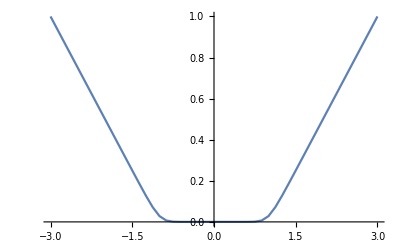

```mathematica
With[{bmax=3,db=1/8,m=2},ListLinePlot[Table[{b,gs[b,m][[1,2]]-gs[b,m][[1,1]]},{b,-bmax,bmax,db}]]]
```

#### overlap with asymptotic wavefunctions

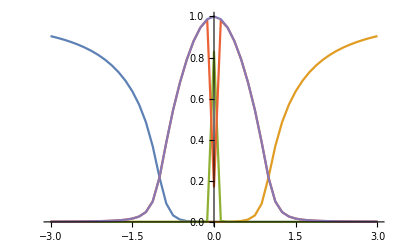

```mathematica
With[{bmax=3,db=1/8,m=2},ListLinePlot[Table[{{b,Abs[gsminusinf.gs[b,m][[2,1]]]^2},{b,Abs[gsplusinf.gs[b,m][[2,1]]]^2},{b,Abs[((gs0up-gs0dn)/(√2)).gs[b,m][[2,1]]]^2},{b,Abs[((gs0up+gs0dn)/(√2)).gs[b,m][[2,1]]]^2},{b,Abs[((gs0up-gs0dn)/(√2)).gs[b,m][[2,1]]]^2+Abs[((gs0up+gs0dn)/(√2)).gs[b,m][[2,1]]]^2}},{b,-bmax,bmax,db}]//Transpose]]
```

#### magnetization

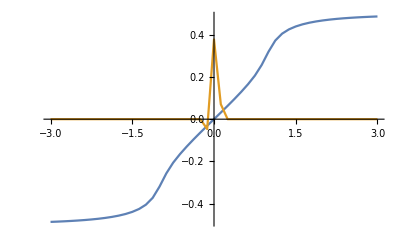

```mathematica
With[{bmax=3,db=1/8,m=2},ListLinePlot[Table[{{b,mx[b,m,1]},{b,mz[b,m,1]}},{b,-bmax,bmax,db}]//Transpose]]
```

#### correlations

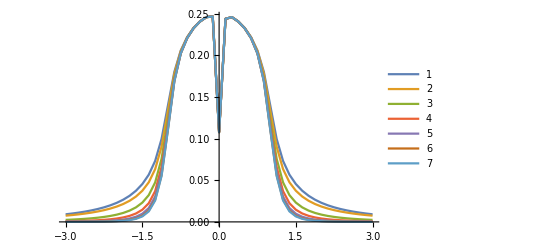

```mathematica
With[{bmax=3,db=1/8,m=2},ListLinePlot[Table[{b,c[b,m,{1,1+δ}]},{δ,1,7},{b,-bmax,bmax,db}],PlotLegends->Range[7]]]
```

#### reduced density matrices

functions for calculating reduced density matrices: (see ReducedDensityMatrix.nb)

```mathematica
rdm[ψABC_?VectorQ,{dA_Integer/;dA≥1,dB_Integer/;dB≥1,dC_Integer/;dC≥1}]/;Length[ψABC]==dA dB dC:=
With[{P=ArrayReshape[ψABC,{dA,dB,dC}]},
Flatten[Transpose[P,{1,3,2}].ConjugateTranspose[P],{{1,2},{3,4}}]]
traceout[ψ_?VectorQ,d_Integer/;d≥1]/;Divisible[Length[ψ],d]:=rdm[ψ,{1,d,Length[ψ]/d}]
traceout[ψ_?VectorQ,d_Integer/;d≤-1]/;Divisible[Length[ψ],-d]:=rdm[ψ,{Length[ψ]/-d,-d,1}]
```

#### entropy of entanglement

```mathematica
s[0|0.]=0;
s[x_]=-x Log[2,x];
```

```mathematica
EE[S_?SpinQ,ψ_]:=Total[s/@Re[Eigenvalues[traceout[ψ,-Length[ψ]/(2S+1)]]]]
```

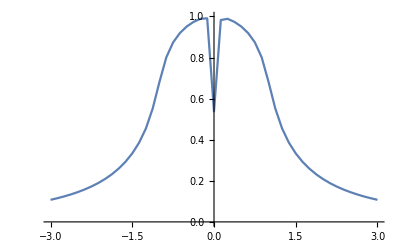

```mathematica
With[{bmax=3,db=1/8,m=2},ListLinePlot[Table[{b,EE[1/2,gs[b,m][[2,1]]]},{b,-bmax,bmax,db}],PlotRange->{0,1}]]
```